{{placeholder→-(gcpms gctm grv)/jmp}}

Stretch factor f=6.05769

1.07302 x-0.0029806 x^2

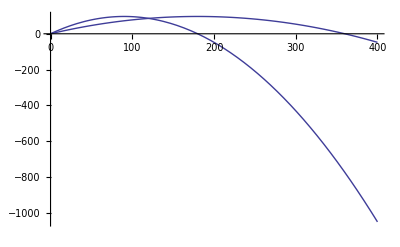

```mathematica
(* Allgemeine Parabelfunktion *)
para[a_,b_,c_,x_]:=a x^2+b x + c;
(* Spielvariablen, mit umgekehrtem Koordinatensystem (y zeigt nach oben) *)
gcGrv=-0.21875;
gcJmp=6.5;
gcPlayerMaxSpeed=6;
gcTimeMultiplier=30;
(* Funktion fuer eine gestreckte Parabel *)
p[t_]:=para[a,b,c,t/placeholder];
(* Wie weit kommt der Spieler in einer Sekunde bei Maximalgeschwindigkeit *)
playerAfterOneSecond=gcPlayerMaxSpeed gcTimeMultiplier;
(* Wie stark musss man die Parabel strecken *)
stretch =placeholder/.Solve[p'[playerAfterOneSecond]==0,placeholder][[1]]/.{a->gcGrv/2,b->gcJmp};
Solve[p'[gcpms gctm]==0/.{a->grv/2,b->jmp},placeholder]
StringForm["Stretch factor f=``",stretch]
para[a,b,c,x/stretch]/.{a-> gcGrv/2,b->gcJmp,c->0}
Plot[{para[a,b,c,x/(stretch )],para[a,b,c,x/(stretch / 2)]}/.{a-> gcGrv/2,b->gcJmp,c->0},{x,0,400}]
```